## 3D PhaseDiagram

```mathematica
Clear["Global`*"]
```

This is the full Hamiltonian having four tunable parameters. We first rescale this parameters by C, which does not change the phase diagram. Then three parameter remains, that is, Δ/C, γ/C, and Ω/C.

```mathematica
hamfull[Δ_,γ_,c_,Ω_]:=Evaluate[{{Δ-I γ,-c,Ω/2},{-c,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
hamfull[Δ,γ,c,Ω]//MatrixForm
Expand@Simplify[Evaluate[Simplify[Discriminant[Det[hamfull[Δ,γ,c,Ω]-e IdentityMatrix[3]],e]]]]
```

(-ⅈ γ+Δ | -c | Ω/2
-c | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

4 c^6-12 c^4 γ^2+12 c^2 γ^4-4 γ^6-8 c^4 Δ^2+16 c^2 γ^2 Δ^2-8 γ^4 Δ^2+4 c^2 Δ^4-4 γ^2 Δ^4+6 c^4 Ω^2-12 c^2 γ^2 Ω^2+6 γ^4 Ω^2+18 c^3 Δ Ω^2-18 c γ^2 Δ Ω^2+10 c^2 Δ^2 Ω^2-10 γ^2 Δ^2 Ω^2-2 c Δ^3 Ω^2-(15 c^2 Ω^4)/4-3 γ^2 Ω^4-9/2 c Δ Ω^4+(Δ^2 Ω^4)/4+Ω^6/2

## Full phase diagram in three-level system

```mathematica
ham[Δ_,γ_,c_]:=Evaluate[{{Δ-γ*I ,-c,1},{-c,Δ+γ*I ,1},{1,1,0}}];
ham[Δ,γ,c]//MatrixForm
```

(-ⅈ γ+Δ | -c | 1
-c | ⅈ γ+Δ | 1
1 | 1 | 0)

```mathematica
EP2Surf[Δ_,γ_,c_]:=Simplify[Discriminant[Det[ham[Δ,γ,c]-IdentityMatrix[3]e],e]]
EP2Surf[Δ,γ,c]
```

4 (8+c^6-γ^6+18 c^3 Δ+Δ^2+c^4 (6-3 γ^2-2 Δ^2)-2 γ^4 (-3+Δ^2)-2 c Δ (9+9 γ^2+Δ^2)-γ^2 (12+10 Δ^2+Δ^4)+c^2 (-15+3 γ^4+10 Δ^2+Δ^4+4 γ^2 (-3+Δ^2)))

```mathematica
Collect[-Det[ham[Δ,γ,c]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,γ,c]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,γ,c]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,γ,c]-IdentityMatrix[3]e],e],e,0];
```

2 c+e^3+2 Δ-2 e^2 Δ+e (-2-c^2+γ^2+Δ^2)

```mathematica
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

27 c+9 Δ-9 c^2 Δ+9 γ^2 Δ+Δ^3

```mathematica
P1=Show[ContourPlot3D[Evaluate[EP2Surf[Δ,γ,c]]==0,{Δ,-1,0.5},{γ,0,3},{c,0,3.8},PlotPoints->100,Mesh->None,PlotRange->All,ContourStyle->Directive[Lighter@Blue,Opacity[0.7],Lighting->"Accent"]],
Frame->True,AxesLabel->{"Δ/Ω","γ/Ω","C/Ω"},Boxed->True,AxesStyle->Directive[Black,18],ImageSize->300]
```

-Graphics3D-

```mathematica
RealSurf=ContourPlot3D[ReEquSurf==0,{Δ,-1,0.5},{γ,0,3},{c,0,3.8},RegionFunction->Function[{x,y,z},Evaluate[EP2Surf[x,y,z]<0]],RegionBoundaryStyle->None,ContourStyle->{Lighter@Green,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
CDeltaSurf=ContourPlot3D[c==-Δ,{Δ,-1,1},{γ,0,3},{c,0,3.8},RegionBoundaryStyle->None,ContourStyle->{Lighter@Red,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
Show[P1,RealSurf,CDeltaSurf,PlotRange->All]
```

-Graphics3D-

```mathematica
EP3EqG=FactorList[Simplify[Resultant[EP2Surf[Δ,γ,c],ReEquSurf,c]]];
EP3ProjLineG=EP3EqG[[2,1]];
EP3G0=FactorList[EP2Surf[Δ,γ,0]];
ReEquSurf0 = FactorList[9 Δ+9 γ^2 Δ+Δ^3]
EP3ProjLineG=EP3EqG[[2,1]]
EP3G0[[2,1]]
```

{{1,1},{Δ,1},{9+9 γ^2+Δ^2,1}}

-1458+729 γ^2-972 Δ^2-216 Δ^4-16 Δ^6

-8+12 γ^2-6 γ^4+γ^6-Δ^2+10 γ^2 Δ^2+2 γ^4 Δ^2+γ^2 Δ^4

```mathematica
P3=Show[ContourPlot[{EP3ProjLineG==0},{Δ,-1,0},{γ,0,3},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]}}],
ContourPlot[{EP3G0[[2,1]]==0},{Δ,-1,0.5},{γ,0,3},PlotPoints->50,ContourStyle->{{RGBColor[0,.3,.7,1],Thickness[0.01]}}],
ContourPlot[{ReEquSurf0[[2,1]]==0},{Δ,-1,0.5},{γ,0,3},PlotPoints->50,ContourStyle->{{RGBColor[0,0.8,0,1],Thickness[0.01]}}],
ContourPlot[{ReEquSurf0[[2,1]]==0},{Δ,-1,0.5},{γ,0,3},PlotPoints->50,ContourStyle->{{RGBColor[0,0.8,0,1],Thickness[0.01]}}]];
```

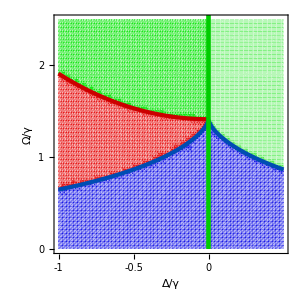

```mathematica
P4=Show[
RegionPlot[ReEquSurf0[[3,1]]>0 && EP3G0[[2,1]]>0,{Δ,0,0.5},{γ,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.1]}],
RegionPlot[ReEquSurf0[[3,1]]>0 && EP3ProjLineG>0,{Δ,-1,0},{γ,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.3]}],
RegionPlot[EP3ProjLineG<0 &&EP3G0[[2,1]]>0,{Δ,-1,0},{γ,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0.9,0,0,.3]}],
RegionPlot[EP3ProjLineG<0 &&EP3G0[[2,1]]<0,{Δ,-1,0.5},{γ,0,2.5},
BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,0.9,.3]}],
P3,Frame->True,FrameLabel->{"Δ/γ","Ω/γ"},PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{-1,-0.5,0},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1,0.5},{0,2.5}},ImageSize->300]
```